# Functions for Global Optimization

## A. GetVariance[ns,nph] function - gets variance expression post ns shots

```mathematica
GetVariance[NumShots_,NumPhotons_]:=
Block[{(*all variables in this function are global*)},
(*We first calculate the probabilities for the first shot then change index of s to the shot number*)
(*This block outputs the matrix of probabilities for multiple photons and 2 shots, row represents shot number*)
Clear[γs1,r,φ,θ,Pmϕ,Pm0ϕs1,Pm0ϕs2, Pm1ϕs1,Pm1ϕs2,Δ,run];
Clear["θ*"];
Clear["r*"];
(*Set accuracy*)
accuracy = 5;
(*number of shots*)
ns=NumShots;
(* Number of Photons *)
nph =NumPhotons;
(* Flat Prior P(ϕ)*)
Pϕ = 1/Δ;
(* creation Subscript[a, 1] out† and Subscript[a, 2 out]†*)
aDagger = {a1Dagger, a2Dagger};
(* annihilation*)
a = {a1,a2};
(*rk here represents Subscript[r, k],magnitude of input state coefficient*)
r=Table[Table[Symbol["r"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*θk here represents Subscript[θ, k],real phase of input state coefficient(exponent)*)
θ=Table[Table[Symbol["θ"<>ToString[k]<>"s"<>ToString[l]],{k,0,nph}],{l,1,ns}];
(*Subscript[φ, k] here represents Subscript[ϕ̃, k] or the unbiased phase estimator*)
φ=Table[Table[Symbol["φm"<>ToString[l]<>"m"<>ToString[n]],{l,0,nph}],{n,0,nph}];
(*Pmxϕsy represent the conditional probability: mx-> x^th outcome, sy-> y^th shot*)
Pmϕ = Table[Table[Symbol["Pm"<>ToString[k]<>"ϕs"<>ToString[n]],{k,0,nph}],{n,1,ns}];
(*Final beamsplitter*)
MatrixForm[u2s1={{Cos[γs1], Sin[γs1]},{-Sin[γs1],Cos[γs1]}}];
ketΨp=∑_(n=0)^nph (r⟦1,n+1⟧ ⅇ^(ⅈ θ⟦1,n+1⟧) ⅇ^(ⅈ (nph-n) ϕ) x1^(nph-n) x2^n)/(√n! √(nph-n)!);
(*Matrix multiplication substitution*)
sub2={x1->u2s1⟦1,1⟧a1Dagger+u2s1⟦2,1⟧a2Dagger,x2->u2s1⟦1,2⟧a1Dagger+u2s1⟦2,2⟧a2Dagger};
(*a1dagger goes to a1*)
sub3=Table[aDagger⟦n⟧->a⟦n⟧,{n,1,2}];
(*Phase sign change due to complex conjugation*)
sub4={ϕ->-ϕ};
(*Phase sign change due to complex conjugation*)
sub5=Table[Table[θ⟦k,n⟧->-θ⟦k,n⟧,{n,1,nph+1}],{k,1,ns}];
(*the ket mentioned below is at |ψ'''>, after the final beamsplitter*)
ketΨppp=ketΨp/.sub2;
braΨppp=ketΨppp/.sub3/.sub4/.sub5;
γs1 = Pi/4;
(*multiply coefficients of braΨppp *)
bracket=Table[(nph-n)!*n!*Coefficient[braΨppp ketΨppp,a1Dagger^n a2Dagger^(nph-n)a1^n a2^(nph-n)],{n,0,nph}];
(*Assigning values from the bracket matrix to the Probability matrix*)
MatrixForm[Table[Pmϕ[[1,n]]=bracket[[n,1]],{n,1,nph+1}] ];
(*This should show probabilities for shot 1 only*)
(*MatrixForm[Pmϕ];*)
(*Rows of Pmϕ correspond to shots and columns correspond to different outcomes*)
(*Pmϕ[[shot#, outcome#]]*)
(*Changing s1 to ss for all values of Pmϕ[[1,k]] to Pmϕ[[s,k]]*)
Subs = Table[Table[{r[[1,k]]-> r[[s,k]],θ[[1,k]]-> θ[[s,k]]},{k,1,nph+1}],{s,2,ns}];
(*Implimenting the substitution*)
Table[Table[Pmϕ[[shot,n]] = Pmϕ[[1,n]]/.Flatten[Subs[[shot-1]]],{n,1,nph+1}],{shot,2,ns}];
(*Clears elements of listOfϕ and listOfPmϕ for another run*)
Clear["ϕm*"];
(*List of possible outcomes as a list of strings - m0, m1 and so on...*)
AllOutcomes = Table[ToString[Symbol["m"<>ToString[n]]],{n,0,nph}];
(*Declaring all phase estimators*)
(*Starts with the base case of ϕ*)
ϕ1st ={"ϕ"} ;
(*Appends all possible m# to ϕ as shots require*)
(*e.g if ns=3 then this creates ϕm0m0m0, ϕm0m0m1 and so on*)
Table[ϕ1st = Outer[StringJoin,ϕ1st,AllOutcomes],ns];
(*Flattening this weird list of lists*)
listOfϕ=Flatten[ϕ1st];
(*Making each element of this list a symbol of its own, not doing this results in issues later*)
listOfϕ = Table[Symbol[listOfϕ[[j]]],{j,1,(nph+1)^ns}];
(*Need a better method of clearing the values assigned to variables in a list*)
Clear["aϕ*"];
(*Generates a list of dummy phase estimators*)
listOfaϕ =Table[Symbol["a"<>ToString[listOfϕ[[n]]]],{n,1,(nph+1)^ns}];
(*Generate a list of a product of probabilities that matches the outcome sequence*)
(*e.g outcome sequence m0m2m1 has the corresponding product of probabilities attached Pm0ϕs1*Pm2ϕs2*Pm1ϕs3 *)
(*converting trig expression to exponential form is important otherwise some parts later don't run*)
listOfPmϕ =Flatten[Outer[Times,Sequence@@Pmϕ]];
(*change this line*)
(*Split expressions into ϕ-dependent and ϕ-indepedent terms*)
(*Collecting terms by changing variables*)
If[nph==1,expr=Table[Table[Coefficient[listOfPmϕ[[n]],Exp[ⅈ ϕ],k],{k,0,ns*nph}],{n,1,(nph+1)^ns}];,
zzz=Table[Collect[listOfPmϕ[[n]]/.ϕ->Log[q]/I,q],{n,1,(nph+1)^ns}];
(*selecting correct coefficients for the correct exponent*)
GetOrder=Table[Table[Exponent[zzz[[n,j]],q],{j,1,Length[zzz[[n]]]}],{n,1,(nph+1)^ns}];
(*Find the ordering that sorts the lists*)
SetOrder=Table[Ordering[GetOrder[[n]]],{n,1,(nph+1)^ns}];
(*Converting sums into a list,because operators disturb the implementation of the ordering*)
zzzlist=Table[Flatten[Table[List[zzz[[m,n]]],{n,1,Length[zzz[[m]]]}]],{m,1,(nph+1)^ns}];
(*Check*)
(*Table[Table[Exponent[zzzlist[[n,j]],q],{j,1,Length[zzzlist[[n]]]}],{n,1,(nph+1)^ns}]*)
(*Implementing the ordering*)
zzzrearranged=Table[Flatten[Table[List[zzzlist[[m,n]]],{n,1,Length[zzzlist[[m]]]}]][[SetOrder[[m]]]],{m,1,(nph+1)^ns}];
(* Check*)(*exponentsRearranged=Table[Table[Exponent[zzzrearranged[[n,j]],q],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];*)

(*Select positive exponents only*)
zzzselect=Table[Table[If[Exponent[zzzrearranged[[n,j]],q]<0,zzzrearranged[[n,j]]=0,zzzrearranged[[n,j]]],{j,1,Length[zzzrearranged[[n]]]}],{n,1,(nph+1)^ns}];
(*Delete the elements which match 0 (terms with negative exponent )*)
zzzselect=Table[DeleteCases[zzzselect[[n]],0],{n,1,(nph+1)^ns}];
(*Look-up table for zzzselect*)
exponentsSelected=Table[Table[Exponent[zzzselect[[n,j]],q],{j,1,Length[zzzselect[[n]]]}],{n,1,(nph+1)^ns}];
expr=zzzselect;];
(*If nph is even then run the next section, *)
If[EvenQ[nph],
(*Continue running if nph is even: to account for the abnormality of the middle term*)
middleTerm=((nph+1)^ns+1)/2;
numberOf0s=Count[exponentsSelected[[middleTerm]],0];
(*Give middleTerm the same dimensionality of the previous array*)
expr[[middleTerm]]=expr[[middleTerm-1]];
(*Check/Look-up table*)
(*Table[Exponent[expr1[[middleTerm,j]],q],{j,1,Length[expr1[[middleTerm]]]}]*)

(*collect all constants and put them in the 1st cell*)
expr[[middleTerm,1]]=Sum[zzzselect[[middleTerm,j]],{j,1,numberOf0s}];
(*Check/Look-up table*)
(* Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*collect all coefficients for even kth exponents and overwrite them in the 2k+1th cell*)
Table[expr[[middleTerm,2i+1]]=zzzselect[[middleTerm,numberOf0s+i]],{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*all coefficients for odd exponents set to 0 and overwrite them in the 2kth cell*)
Table[expr[[middleTerm,2i]]=0,{i,1,ns*nph/2}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)

(*Drop terms after the last if there are - There might not be...need to check, since we took care of dimensionality earlier*)
expr[[middleTerm]]=Drop[expr[[middleTerm]],{ns*nph+2,Length[expr[[middleTerm]]]}];
(*Check/Look-up table*)
(*Table[Exponent[expr[[middleTerm,j]],q],{j,1,Length[expr[[middleTerm]]]}]*)
(*else leave the expression alone*)
,expr];
(*Check*)
exponentsSelected2=Table[Table[Exponent[expr[[n,j]],q],{j,1,Length[expr[[n]]]}],{n,1,(nph+1)^ns}];
(*Print[exponentsSelected2];*)

expr=expr/.q->1;
(*expr[[n,k+1]] n is outcome number and k+1 is the coefficient of e^ikϕ*)
(*Splitting constant terms from the others and adding complex conjugate terms to the other - This is a check, not to be fed into the integral-*)
(* exprSplit =Table[expr[[n,1]]+2*Sum[expr[[n,k+1]]*E^(ⅈ k ϕ),{k,1,ns*nph}],{n,1,(nph+1)^ns}];*)
(*This list contains all the phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
listOfϕ1=ParallelTable[Re[(2*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}])]/Re[(expr[[n,1]]*Δ+2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}])],{n,1,(nph+1)^ns}];
(*ParallelTable or something causes listOfϕ to get the order reversed as per our conventions, reverting it back*)
(*We calculate the final variance using the dummy phase estimators*)
(*Removed integration and substituted pre-calculated integrals*)
(*This list contains all the variance values*)
listOfPartialVariance1 = ParallelTable[Pϕ*Re[expr[[n,1]]*(Δ^3/12)+2*Sum[expr[[n,k+1]]*((4 k Δ Cos[(k Δ)/2]+(-8+k^2 Δ^2) Sin[(k Δ)/2])/(2 k^3)),{k,1,ns*nph}] -4*listOfaϕ[[n]]*Sum[expr[[n,k+1]]*-((ⅈ (k Δ Cos[(k Δ)/2]-2 Sin[(k Δ)/2]))/k^2),{k,1,ns*nph}]+Δ*expr[[n,1]]*listOfaϕ[[n]]^2+2*listOfaϕ[[n]]^2*Sum[expr[[n,k+1]]*((2 Sin[(k Δ)/2])/k),{k,1,ns*nph}] ],{n,1,(nph+1)^ns}];
(*We calculated the final variance using the dummy phase estimators - listOfaϕ*)
(*And then replace the dummy phase estimators in 1.3.3 by the real ones calculated in 1.3.2*)
dummyFinalVariance1=Flatten[listOfPartialVariance1/.{Table[listOfaϕ[[n]]-> listOfϕ1[[n]],{n,1,(nph+1)^ns}]},1];

(*Normalizing the variance, each product normalizes 1 probability term in the product (of listOfPmϕ); e.g (1 /(r0s1^2+r1s1^2+r2s1^2)) normalizes Pm#ϕs1*)
normalizationTerm = ∏_(i=1)^ns 1/(∑_(s=1)^(nph+1) (r[[i,s]])^2);
(*Final variance*)
(*Sum is replaced by ParallelSum to decrease the time of computation*)
(*Note: We are ommitting Pϕ here since we have already taken that into consideration earlier while constructing dummyfinalvariance*)
finalVariance= normalizationTerm*Sum[dummyFinalVariance1[[j]], {j,1,(nph+1)^ns}];
(*While the imaginary term is essentially 0, mathematica may be calculating some expressions analytically and would keep ~0 imaginary values, therefore neglecting those*)
finalVariance = Re[finalVariance];
(* Print[finalVariance]; *)
Return[finalVariance]
(*Manual sanity check - Need to make it automatic*)
(*Print[Simplify[finalVariance/.{r0s1-> 1,r1s1-> 0,r2s1-> 0,r0s2-> 1,r1s2-> 0,r2s2-> 0},Assumptions-> Δ∈Reals]];*)]
```

## B. ExtractOptState[Δ] Function - optimizes variance in A.

(*In case it takes too long change this version from 2.5 in that it simplifies optimization taking symmetry of states into account *)

```mathematica
ExtractOptState[delta_]:=
(*Block or Module*)
Block[{Δ,OptimalrValues,variablelist,ListOfOptimalrValues,variablelistrandom,nrun,iteration,OptimalVariance,listforfindminimum,listOfLocalMinVariance,IndexMinVar},(*{"θ*","r*",(*list variables to keep local*)}*)
(*Generate a list to optimize over*)
Δ=delta;
variablelist = Flatten[{θ,r}];
(*Generate a list of dummy optimization variable to assign a random starting point to them*)
variablelistrandom = ParallelTable[Symbol[ToString[variablelist[[l]]]<>"dummy"],{l,1,2*ns*(nph+1)}];
(*Give a random starting point to each dummy variable; θs are between -π and π while rs are between 0 and 1*)
(*run 50 iterations of findminimum*)
nrun=20;
iteration=ParallelTable[
SeedRandom[];
Table[variablelistrandom[[n]] =RandomReal[{-π,π}],{n,1,ns*(nph+1)}];
Table[variablelistrandom[[n]] =RandomReal[{0,1}],{n,ns*(nph+1)+1,2*ns*(nph+1)}];
(*Arranging listforfindminimum to match FindMinimum syntax*)
listforfindminimum = Table[{variablelist[[n]],variablelistrandom[[n]]},{n,1,2*ns*(nph+1)}];
(*Optimization*)
FindMinimum[finalVariance,listforfindminimum,AccuracyGoal-> 5],{n,1,nrun}];
(*lower accuracy in case it takes too long*)
(*Finds the minimum from list of local minimums*)
listOfLocalMinVariance=Table[iteration[[n,1]],{n,1,nrun}];
IndexMinVar =Position[listOfLocalMinVariance,Min[listOfLocalMinVariance]]⟦1,1⟧;
(*OptimalVariance={optimal variance,{optimal state}*)
OptimalVariance={iteration[[IndexMinVar,1]],Table[iteration[[IndexMinVar,2,n]],{n,1,Length[iteration[[IndexMinVar,2]]]}]};
(*Return OptimalVariance[[1]] if wanting to use optimal variance (numerical value) *)
(*Return[OptimalVariance[[1]]];*)
(*Return OptimalVariance if wanting to use optimal variance (numerical value) along with the optimal states*)
(*Return[OptimalVariance];*)
(*Extract minvalues for r variables*)
ListOfOptimalrValues=Table[OptimalVariance[[2,n,2]],{n,ns*(nph+1)+1,Length[OptimalVariance[[2]]]}];
(*Partition lists into seperate shots*)
OptimalrValues=Partition[ListOfOptimalrValues,nph+1];
(*Normalizing over multiple shots*)
OptimalrValues = Table[Abs[Normalize[OptimalrValues[[n]]]],{n,1,ns}];
(*Return OptimalrValues if wanting to print optimal input state amplitudes and construct boundaries*)
Return[OptimalrValues]
]
```

## C. Plug States - no optimization

### VarRatioOptimal

```mathematica
GetOpt[]:=Block[{},VarRatioOpt=Table[Δ =n*π/10;
finalVarianceOpt=ExtractOptState[Δ];
finalVarianceOpt[[1]]/(Δ^2/12)
(*,{n,{1,3,5,10}}];*)
,{n,{3}}];
(*,{n,1,10}];*)
Return[VarRatioOpt];]
```

```mathematica
finalVarianceOpt
```

{{0.707107,4.49954×10^-8,6.82694×10^-8,1.04706×10^-7,0.707107}}

### Plug in N00N states and compare optimal variance with the new variance

```mathematica
PlugN00N[]:=
Block[{},
VarRatioN00N=Table[
Δ =n/10*π;
(*feed in θ values*)
sublistN00Nθ = Table[Table[θ[[n,i]] ->  RandomReal[{-π,π}],{i,1,nph+1}],{n,1,ns}];
Table[sublistN00Nθ[[n,nph+1,2]]= sublistN00Nθ[[n,1,2]]-π/2,{n,1,ns}];
sublistN00Nθ;
(*feed in r values*)
sublistN00Nr=Table[Table[If[i==1 ||i==nph+1,r[[n,i]]-> 1/(√2) ,r[[n,i]]->0 ],{i,1,nph+1}],{n,1,ns}];
substlistN00N = Flatten[{sublistN00Nθ, sublistN00Nr}];
finalVarianceN00N=finalVariance/.substlistN00N;
(*Print[finalVarianceN00N/finalVarianceN00NOpt];*)
finalVarianceN00N/(Δ^2/12)
,{n,{3}}];
Return[VarRatioN00N];]
```

### Plug in Gaussian (G2) State by optimizing over ρ

```mathematica
PlugG2[]:=
Block[{},
VarRatioG2=Table[
Δ =num/10*π;
ρ3 = Table[Symbol["ρ3s"<>ToString[n]],{n,1,ns}];
ψG2r =Table[Table[(E^(-ρ3[[n]](k-nph/2)^2))/(√(∑_(kprime=0)^nph (E^(-ρ3[[n]](kprime-nph/2)^2))^2)),{k,0,nph}],{n,1,ns}];
ψG2θ=Table[Table[ k (π/2),{k,0,nph}],{n,1,ns}];
substlistG2r=Table[Table[r[[n,i]]-> ψG2r[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG2θ = Table[Table[θ[[n,i]]-> ψG2θ[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG2= Flatten[{substlistG2r,substlistG2θ}];
finalVariance3=finalVariance/.substlistG2;
variablelist3 = Flatten[List[ρ3]];
variablelistrandom3 = Table[Symbol[ToString[variablelist3[[l]]]<>"dummy"],{l,1,ns}];
nrun=5;
iteration=Table[
Table[variablelistrandom3[[n]] =-4,{n,1,ns}];
(*Arranging listforfindminimum to match FindMinimum syntax*)
listforfindminimum3 = Table[{variablelist3[[n]],variablelistrandom3[[n]]},{n,1,ns}];
(*Optimization subject to constraint to avoid unphysical solutions*)
FindMinimum[{finalVariance3,ρ3[[1]]>0 (*&& ρ3[[2]]>0 && ρ3[[3]]>0*)},listforfindminimum3],nrun];
listOfLocalMinVariance=Table[iteration[[n,1]],{n,1,nrun}];
IndexMinVar =Position[listOfLocalMinVariance,Min[listOfLocalMinVariance]]⟦1,1⟧;
finalVarianceG2={iteration[[IndexMinVar,1]],Table[iteration[[IndexMinVar,2,n]],{n,1,Length[iteration[[1,2]]]}]};
(*Print[OptimalVarianceQG2];*)
(*this prints out optimized ρ*)
(*finalVarianceG2[[2]]*)
finalVarianceG2[[1]]/(Δ^2/12)
,{num,{3}}];
(*,{num,1,10}];*)
Return[VarRatioG2];];
```

### Plug in QuasiGaussian (QG2) State by optimizing over ρ and ρprime

```mathematica
PlugQG2[]:=
Block[{},VarRatioQG2=Table[
	Δ =num/10*π;
(*Clear[ρ2,ρprime2];*)
ψQG2r =Table[(E^(-ρ2(k-nph/2)^2-ρprime2(k-nph/2)^4))/(√(∑_(kprime=0)^nph (E^(-ρ2(kprime-nph/2)^2-ρprime2(kprime-nph/2)^4))^2)),{k,0,nph}];
ψQG2θ=Table[ k (π/2),{k,0,nph}];
substlistQG2r=Table[r[[1,i]]-> ψQG2r[[i]],{i,1,nph+1}];
substlistQG2θ = Table[θ[[1,i]]-> ψQG2θ[[i]],{i,1,nph+1}];
substlistQG2= Flatten[{substlistQG2r,substlistQG2θ}];
finalVariance2=finalVariance/.substlistQG2;
ρρprime2 = List[ρ2,ρprime2];
variablelist2 = Flatten[{ρρprime2}];
variablelistrandom2 = Table[Symbol[ToString[variablelist2[[l]]]<>"dummy"],{l,1,2}];
nrun=10;
iteration=Table[
SeedRandom[];
Table[variablelistrandom2[[n]] =RandomReal[{0,1}],{n,1,2}];
(*Arranging listforfindminimum to match FindMinimum syntax*)
listforfindminimum2 = Table[{variablelist2[[n]],variablelistrandom2[[n]]},{n,1,2}];
(*Optimization*)
FindMinimum[finalVariance2,listforfindminimum2],nrun];
(*lower accuracy in case it takes too long*)
listOfLocalMinVariance=Table[iteration[[n,1]],{n,1,nrun}];
IndexMinVar =Position[listOfLocalMinVariance,Min[listOfLocalMinVariance]]⟦1,1⟧;
finalVarianceQG2={iteration[[IndexMinVar,1]],Table[iteration[[IndexMinVar,2,n]],{n,1,Length[iteration[[1,2]]]}]};
(*Print[OptimalVarianceQG2];*)
(*this prints out optimized ρ and ρprime values*)
(*finalVarianceQG2[[2]]*)
finalVarianceQG2[[1]]/(Δ^2/12),{num,1,10}];
Return[VarRatioQG2];];
```

### Plug in Gaussian (G1) c_p≃0.16, ρ≃c_p Δ/N

```mathematica
PlugG1[]:=
Block[{},Clear[ρ2,ρ3,ρprime2];
VarRatioG1=Table[
	Δ =num/10*π;
ρ3 = Table[Symbol["ρ3s"<>ToString[n]],{n,1,ns}];
Table[ρ3[[n]]=0.16Δ/nph;,{n,1,ns}];
ψG1r =Table[Table[(E^(-ρ3[[n]](k-nph/2)^2))/(√(∑_(kprime=0)^nph (E^(-ρ3[[n]](kprime-nph/2)^2))^2)),{k,0,nph}],{n,1,ns}];
ψG1θ=Table[Table[ k (π/2),{k,0,nph}],{n,1,ns}];
substlistG1r=Table[Table[r[[n,i]]-> ψG1r[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1θ = Table[Table[θ[[n,i]]-> ψG1θ[[n,i]],{i,1,nph+1}],{n,1,ns}];
substlistG1= Flatten[{substlistG1r,substlistG1θ}];
finalVarianceG1=finalVariance/.substlistG1;
(*Print[OptimalVarianceQG2];*)
(*this prints out optimized ρ and ρprime values*)
(*finalVarianceQG2[[2]]*)
finalVarianceG1/(Δ^2/12)
,{num,{3}}];
(*,{num,1,10}];*)
Return[VarRatioG1];];
```

# Non-Adaptive Global Optimization Method

## 1. Plotting 1 shot and 2 shot optimal states and compare the two

## 1 shot optimal states

#### Optimal states for Nph = 10 for different prior Δ

```mathematica
GetVariance[1,10]
```

Re[(Re[(((14175 1)/4+4+(7875 1)/4) Δ^3)/172800+1/(3600 1)-1+1/1+2 (((1) (1))/230400+5)]/Δ+Re[1/362880+4+2 (1)]/Δ+Re[1]/Δ+1/Δ+3+1/Δ+Re[1]/Δ+Re[1]/Δ+Re[((1) Δ^3)/207360+4+2 (1)]/Δ)/(r0s1^2+r10s1^2+r1s1^2+r2s1^2+r3s1^2+r4s1^2+r5s1^2+r6s1^2+r7s1^2+r8s1^2+r9s1^2)]
 |  |  |  |

```mathematica
plots=Table[Flatten[ExtractOptState[n π/10]],{n,{1,2,3,4,5,10}}];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
Show[ListLinePlot[plots[[1]],PlotStyle->{Orange,Thick},PlotLegends->Placed[{π/10},{Below,Center}]],ListLinePlot[plots[[2]],PlotStyle->{Gray,Dashed},PlotLegends->Placed[{(2π)/10},{Below,Center}]],ListLinePlot[plots[[3]],PlotStyle->Dotted,PlotLegends->Placed[{(3π)/10},{Below,Center}]],ListLinePlot[plots[[4]],PlotStyle->Dotted,PlotLegends->Placed[{(4π)/10},{Below,Center}]],ListLinePlot[plots[[5]],PlotStyle->Blue,PlotLegends->Placed[{(5π)/10},{Below,Center}]],ListLinePlot[plots[[6]],PlotStyle->{Magenta,Thick},PlotLegends->Placed[{π},{Below,Center}]],PlotRange->{{1,11},{0,0.7}}, Frame->True,PlotLabel->"|r_k| for different prior uncertainties for N=10",FrameLabel->{"",Style["|r_k|",Thick]}, FrameTicks->{{Automatic,Automatic},{{{1,"0,10"},{3,"2,8"},{5,"4,6"},{7,"6,4"},{9,"8,2"},{11,"10,0"}},Automatic}}]
```

-Graphics-

## 2 shot optimal states

#### Compare 2 shot optimal states with 1 shot optimal states for 4 photons

```mathematica
GetVariance[1,4];
```

```mathematica
plotcompare1=Table[Flatten[ExtractOptState[n π/10]],{n,{1,5,10}}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

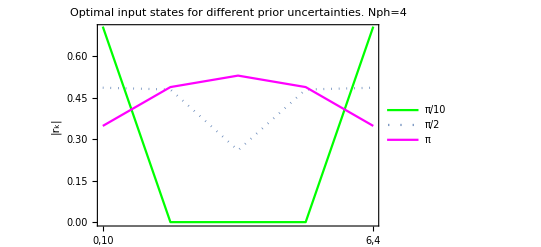

```mathematica
Show[ListLinePlot[plotcompare1[[1]],PlotStyle->{Green,Thick},PlotLabel->"Optimal input states for different prior uncertainties. Nph=4",PlotLegends->{π/10}],ListLinePlot[plotcompare1[[2]],PlotStyle->Dotted,PlotLegends->{(5π)/10}],ListLinePlot[plotcompare1[[3]],PlotStyle->Magenta,PlotLegends->{(10π)/10}],Frame->True,FrameLabel->{"",Style["|r_k|",Thick]}, FrameTicks->{{Automatic,Automatic},{{{1,"0,10"},{3,"8,2"},{5,"6,4"},{7,"4,6"},{9,"2,8"},{11,"0,10"}},Automatic}},PlotRange->{{1,5},{0,0.7}}]
```

```mathematica
GetVariance[2,4];
```

```mathematica
plotcompare2=Table[Flatten[ExtractOptState[n π/10]],{n,{1,5,10}}];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(*Partition lists into seperate shots*)
rchecksplit=Table[Partition[plotcompare2[[n]],nph+1],{n,1,3}]
```

{{{0.707107,8.85196×10^-8,3.97988×10^-7,8.78004×10^-8,0.707107},{0.707107,4.16876×10^-7,1.33792×10^-7,7.36519×10^-8,0.707107}},{{0.639133,4.92878×10^-7,0.427805,4.89628×10^-7,0.639134},{0.458675,0.490077,0.314457,0.490076,0.458676}},{{0.347537,0.489051,0.52924,0.48905,0.347536},{0.347537,0.48905,0.52924,0.489051,0.347537}}}

```mathematica
plotcompare2 = Table[Table[Abs[Normalize[rchecksplit[[m,n]]]],{n,1,ns}],{m,1,3}]
```

{{{0.707107,8.85196×10^-8,3.97988×10^-7,8.78004×10^-8,0.707107},{0.707107,4.16876×10^-7,1.33792×10^-7,7.36519×10^-8,0.707107}},{{0.639133,4.92878×10^-7,0.427805,4.89628×10^-7,0.639134},{0.458675,0.490077,0.314457,0.490076,0.458676}},{{0.347537,0.489051,0.52924,0.48905,0.347536},{0.347537,0.48905,0.52924,0.489051,0.347537}}}

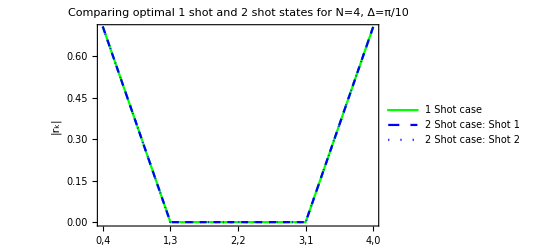

```mathematica
Show[ListLinePlot[plotcompare1[[1]],PlotStyle->{Green,Thick},PlotLegends->Placed[{"1 Shot case"},Below]],ListLinePlot[plotcompare2[[1,1]],PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"2 Shot case: Shot 1"},Below]],ListLinePlot[plotcompare2[[1,2]],PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"2 Shot case: Shot 2"},Below]],Frame->True,PlotLabel->"Comparing optimal 1 shot and 2 shot states for N=4, Δ=π/10",FrameLabel->{"",Style["|r_k|",Thick]}, FrameTicks->{{Automatic,Automatic},{{{1,"0,4"},{2,"1,3"},{3,"2,2"},{4,"3,1"},{5,"4,0"}},Automatic}},PlotRange->{{1,5},{0,0.7}}]
```

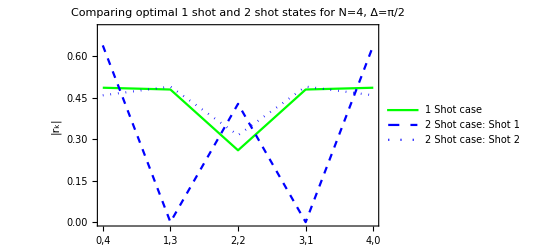

```mathematica
Show[ListLinePlot[plotcompare1[[2]],PlotStyle->{Green,Thick},PlotLabel->"Comparing optimal 1 shot and 2 shot states for N=4, Δ=π/2",PlotLegends->Placed[{"1 Shot case"},Below]],ListLinePlot[plotcompare2[[2,1]],PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"2 Shot case: Shot 1"},Below]],ListLinePlot[plotcompare2[[2,2]],PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"2 Shot case: Shot 2"},Below]],AxesOrigin-> {0,0},Frame->True,FrameLabel->{"",Style["|r_k|",Thick]}, FrameTicks->{{Automatic,Automatic},{{{1,"0,4"},{2,"1,3"},{3,"2,2"},{4,"3,1"},{5,"4,0"}},Automatic}},PlotRange->{{1,5},{0,0.7}}]
```

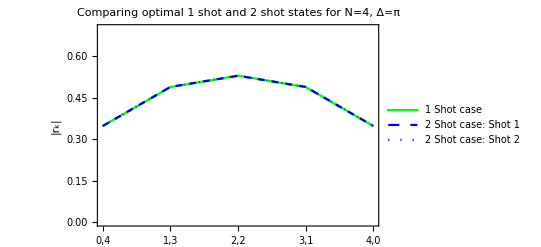

```mathematica
Show[ListLinePlot[plotcompare1[[3]],PlotStyle->{Green,Thick},PlotLabel->"Comparing optimal 1 shot and 2 shot states for N=4, Δ=π",PlotLegends->Placed[{"1 Shot case"},Below]],ListLinePlot[plotcompare2[[3,1]],PlotStyle->{Blue,Dashed},PlotLegends->Placed[{"2 Shot case: Shot 1"},Below]],ListLinePlot[plotcompare2[[3,2]],PlotStyle->{Blue,Dotted},PlotLegends->Placed[{"2 Shot case: Shot 2"},Below]],AxesOrigin-> {0,0},Frame->True,FrameLabel->{"",Style["|r_k|",Thick]}, FrameTicks->{{Automatic,Automatic},{{{1,"0,4"},{2,"1,3"},{3,"2,2"},{4,"3,1"},{5,"4,0"}},Automatic}},PlotRange->{{1,5},{0,0.7}}]
```

# Non-Adaptive Best-Fit State inputs

## 2. Construct boundaries between Gaussian and N00N states

## Algorithm and functions to run

### Algorithm

```mathematica
(*Construct boundary delta for N00N*)
(*call the ExtractOptState function with a prior Δ, this returns the optimal state for the particular Δ*)
(*define isNOON and isQG variables*)
(*set Δ1=π/10 or 0 and Δ2=π*)
(*Run bisection function to return a new Δ to check*)
(*Check if this state is N00N or QG*)
(*run bisection method, given Δ find Δnew that still outputs N00N. Keep tolerance to 10^-2*)
(*bisectN00N returns the boundary Δ for N00N*)
```

### BisectN00N[delta1, delta2] Function

```mathematica
bisectN00N[delta1_,delta2_]:=
Block[{tolerance,Δnew,OptStateNew,HalfOptStateNew,isSymmetric,isN00N,Δ1,Δ2},
tolerance = 10^-2;
Δ1=delta1;
Δ2=delta2;
While[Δ2-Δ1>tolerance,
Δnew = (Δ2+Δ1)/2;(*midpoint*)
(*Print[Δnew];*)
OptStateNew= ExtractOptState[Δnew];
(*Print[OptStateNew];*)
(*Taking only the first half of the optimal states and throwing the rest*)
	HalfOptStateNew=Table[Table[OptStateNew[[s,t]],{t,1,Ceiling[(nph+1)/2]}],{s,1,ns}];
isSymmetric=AllTrue[Flatten[Table[Abs[OptStateNew[[1,1+n]]-OptStateNew[[1,nph+1-n]]]< 10^-5,{n,0,Floor[nph/2]}]],TrueQ];
isN00N=If[isSymmetric==True&&Abs[OptStateNew[[1,1]]-0.70710]<10^-5,True,False];
If[isN00N==True, Δ1=Δnew,Δ2 = Δnew];];
Return[Δ1];];
```

```mathematica
(*Similarly for QG*)
```

### BisectG[delta1, delta2] Function

```mathematica
bisectG[delta1_,delta2_]:=
Block[{tolerance,Δnew,OptStateNew,HalfOptStateNew,isSymmetric,isN00N,isQG,Δ1,Δ2},
tolerance = 10^-2;
Δ1=delta1;
Δ2=delta2;
While[Δ2-Δ1>tolerance,
Δnew = (Δ2+Δ1)/2;(*midpoint*)
(*Print[N[Δnew]];*)
OptStateNew= ExtractOptState[Δnew];
(*Print[OptStateNew];*)
(*Taking only the first half of the optimal states and throwing the rest*)
	HalfOptStateNew=Table[Table[OptStateNew[[s,t]],{t,1,Ceiling[(nph+1)/2]}],{s,1,ns}];
isSymmetric=AllTrue[Flatten[Table[Abs[OptStateNew[[1,1+n]]-OptStateNew[[1,nph+1-n]]]< 10^-5,{n,0,Floor[nph/2]}]],TrueQ];
isN00N=If[isSymmetric==True&&Abs[OptStateNew[[1,1]]-0.70710]<10^-5,True,False];
isG=If[isSymmetric==True&& OrderedQ[HalfOptStateNew[[1]]] (*&& OrderedQ[Differences[HalfOptStateNew[[1]]],Greater]*),True,False];
If[isG==False, Δ1=Δnew,Δ2 = Δnew];];
Return[Δ2];];
```

## Collect boundaries and plot

#### 1 shot N00N and G boundary computation

```mathematica
(*Construct*)
```

```mathematica
ΔN00Nboundary={};
ΔGboundary = {};
Photons = {};
Table[
GetVariance[1,numPho];
AppendTo[Photons,numPho];
AppendTo[ΔN00Nboundary,bisectN00N[0,π]];
AppendTo[ΔGboundary , bisectG[0,π]];
,{numPho,1,20}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

#### 1 shot N00N and G boundary plots

```mathematica
(*Plot*)
```

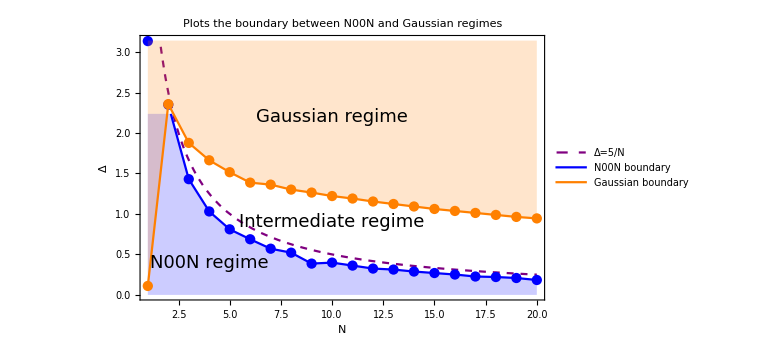

```mathematica
N00Nboundary = Thread[ΔN00Nboundary,Photons];
Gboundary = Thread[ΔGboundary,Photons];
Show[Plot[5/x,{x,0,20}, PlotStyle->{Dashed,Purple},PlotLegends->Placed[{"Δ=5/N"},Bottom]],Plot[1/(√x),{x,0,20}, PlotStyle->{Dashed,Red},PlotLegends->Placed[{"Δ=1/(√N)"},Bottom]],ListPlot[N00Nboundary,PlotStyle->Blue],ListLinePlot[N00Nboundary,PlotLegends->Placed[{"N00N boundary"},Bottom],PlotStyle->Blue,Filling->Bottom],ListPlot[Gboundary,PlotStyle->Orange],ListLinePlot[ΔGboundary,PlotLegends->Placed[{"Gaussian boundary"},Bottom],PlotStyle->Orange,Filling->π],PlotLabel-> "Plots the boundary between N00N and Gaussian regimes",  AxesOrigin->{0,0},Epilog->{Inset[Style["N00N regime",18],{4,0.4}],Inset[Style["Intermediate regime",18],{10,0.9}],Inset[Style["Gaussian regime",18],{10,2.2}]},FrameLabel->{"N","Δ"}, PlotRange->{{1,20},{0,π}},Frame->True ,ImageSize->Large]
```

## 3. Showing why Gaussian states are as good as Quasi-Gaussian states. Only 1 optimization variable instead of 2.

### Compare G, QG with optimized variables for nph = 7 by changing Δ

```mathematica
GetVariance[1,7];
```

```mathematica
VarRatioOpt7 = GetOpt[];
VarQG27 = PlugQG2[];
VarG27=PlugG2[];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

```mathematica
(*Generate the x axis*)
```

```mathematica
Listx = Table[{n,(n π)/10},{n,1,10}];
```

```mathematica
Listx
```

{{1,π/10},{2,π/5},{3,(3 π)/10},{4,(2 π)/5},{5,π/2},{6,(3 π)/5},{7,(7 π)/10},{8,(4 π)/5},{9,(9 π)/10},{10,π}}

```mathematica
VarQG27={0.6849219662957536,0.43344802672783017,0.4224625156201721,0.30528583906362794,0.2329872024364851,0.18565891238415663,0.15358654699167187,0.13083444763904933,0.11489367082969,0.1036839629668639}
```

{0.684922,0.433448,0.422463,0.305286,0.232987,0.185659,0.153587,0.130834,0.114894,0.103684}

```mathematica
VarG27
```

```mathematica
VarG27={0.8670691329374617,0.6272697445392367,0.4321315869924587,0.30926883054982474,0.23402927144765753,0.18568946811527362,0.15390342390499684,0.1319723343284147,0.11667337898881025,0.10579467673583214}
```

{0.867069,0.62727,0.432132,0.309269,0.234029,0.185689,0.153903,0.131972,0.116673,0.105795}

```mathematica
VarRatioOpt7
```

```mathematica
VarRatioOpt7={0.6849219662957731,0.4227048520081297,0.3427565214083784,0.30357091148933596,0.2327421438451329,0.1856569459726369,0.1535669138289248,0.13079702587411704,0.11486290193823946,0.10366807967957914}
```

{0.684922,0.422705,0.342757,0.303571,0.232742,0.185657,0.153567,0.130797,0.114863,0.103668}

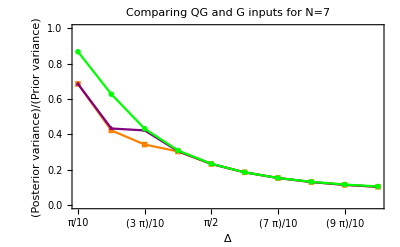

```mathematica
Show[ListLinePlot[VarRatioOpt7,PlotMarkers ->{■,Scaled[0.05]}, PlotStyle->Orange,PlotLegends->Placed[{"Optimal"},{Right,Top}] ],
ListLinePlot[VarQG27,PlotMarkers ->{▲,Scaled[0.05]}, PlotStyle->Purple,PlotLegends->Placed[{"Optimal Quasi-Gaussian"},{Right,Top}]] ,
ListLinePlot[VarG27,PlotMarkers ->{•,Scaled[0.05]}, PlotStyle->Green,PlotLegends->Placed[{"Optimal Gaussian"},{Right,Top}]] ,FrameLabel->{"Δ","(Posterior variance)/(Prior variance)"},PlotLabel-> "Comparing QG and G inputs for N=7", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}}]
```

### Compare G, QG with optimized variables for nph = 13 by changing Δ

```mathematica
GetVariance[1,13];
```

```mathematica
VarRatioOpt13 = GetOpt[];
VarQG213 = PlugQG2[];
VarG213=PlugG2[];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

```mathematica
(*Generate the x axis*)
```

```mathematica
Listx = Table[(n π)/10,{n,1,10}];
```

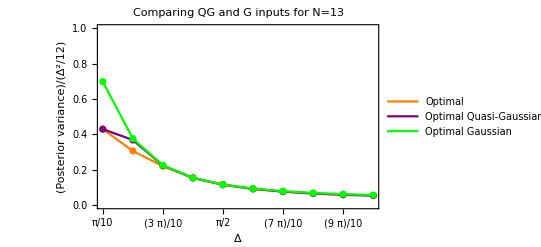

```mathematica
Show[ListPlot[VarRatioOpt13, PlotStyle->Orange],ListLinePlot[VarRatioOpt13, PlotStyle->Orange,PlotLegends->{"Optimal"}] ,
ListPlot[VarQG213, PlotStyle->Purple],ListLinePlot[VarQG213, PlotStyle->Purple,PlotLegends->{"Optimal Quasi-Gaussian"}] ,
ListPlot[VarG213, PlotStyle->Green],ListLinePlot[VarG213, PlotStyle->Green,PlotLegends->{"Optimal Gaussian"}] ,FrameLabel->{"Δ","(Posterior variance)/(Δ^2/12)"},PlotLabel-> "Comparing QG and G inputs for N=13", PlotRange->{{1,10},{0,1}},Frame->True, FrameTicks->{{Automatic,Automatic},{Listx,Automatic}}]
```

## 4. Show that for Gaussians ρ ∝ Δ, and ρ ∝ 1/Nph.

### Showing that ρ ∝ 1/Nph for 1 shot

#### Δ = π

```mathematica
num=5;
ρNphlist=Table[
GetVariance[1,n];
PlugG2[]
,{n,1,num}]
```

{{{ρ3s1→0.}},{{ρ3s1→0.173287}},{{ρ3s1→0.133801}},{{ρ3s1→0.10742}},{{ρ3s1→0.0891177}},{{ρ3s1→0.0759361}},{{ρ3s1→0.0660759}},{{ρ3s1→0.0584464}},{{ρ3s1→0.0523632}},{{ρ3s1→0.0473867}},{{ρ3s1→0.0432269}},{{ρ3s1→0.0396879}},{{ρ3s1→0.0366338}},{{ρ3s1→0.0339678}},{{ρ3s1→0.031619}},{{ρ3s1→0.0295338}},{{ρ3s1→0.0276711}},{{ρ3s1→0.025998}},{{ρ3s1→0.0244883}},{{ρ3s1→0.0231203}},{{ρ3s1→0.0218763}},{{ρ3s1→0.0207411}},{{ρ3s1→0.0197021}},{{ρ3s1→0.0187484}},{{ρ3s1→0.0178706}},{{ρ3s1→0.0170606}},{{ρ3s1→0.0163116}},{{ρ3s1→0.0156173}},{{ρ3s1→0.0149724}}}

```mathematica
ρNphlist=Flatten[ρNphlist]
```

```mathematica
ρNphlist={ρ3s1->0.,ρ3s1->0.17328728150532516,ρ3s1->0.1338014507919026,ρ3s1->0.10741977477730694,ρ3s1->0.08911771443763386,ρ3s1->0.07593608239845716,ρ3s1->0.06607589127373727,ρ3s1->0.05844642000614857,ρ3s1->0.052363185639869296,ρ3s1->0.047386680021342366,ρ3s1->0.04322687264679448,ρ3s1->0.03968786302367982,ρ3s1->0.03663377516767206,ρ3s1->0.033967801014326594,ρ3s1->0.03161897600890751,ρ3s1->0.029533837174348383,ρ3s1->0.02767106034458708,ρ3s1->0.02599797696378185,ρ3s1->0.02448825642518255,ρ3s1->0.02312033201692736,ρ3s1->0.02187630132625215,ρ3s1->0.020741139008419587,ρ3s1->0.01970211805086181,ρ3s1->0.018748374607797547,ρ3s1->0.017870573754153813,ρ3s1->0.017060648190815896,ρ3s1->0.016311590726159734,ρ3s1->0.015617287344911475,ρ3s1->0.014972381408367064}
```

{ρ3s1→0.,ρ3s1→0.173287,ρ3s1→0.133801,ρ3s1→0.10742,ρ3s1→0.0891177,ρ3s1→0.0759361,ρ3s1→0.0660759,ρ3s1→0.0584464,ρ3s1→0.0523632,ρ3s1→0.0473867,ρ3s1→0.0432269,ρ3s1→0.0396879,ρ3s1→0.0366338,ρ3s1→0.0339678,ρ3s1→0.031619,ρ3s1→0.0295338,ρ3s1→0.0276711,ρ3s1→0.025998,ρ3s1→0.0244883,ρ3s1→0.0231203,ρ3s1→0.0218763,ρ3s1→0.0207411,ρ3s1→0.0197021,ρ3s1→0.0187484,ρ3s1→0.0178706,ρ3s1→0.0170606,ρ3s1→0.0163116,ρ3s1→0.0156173,ρ3s1→0.0149724}

```mathematica
ρNphπ=Table[ρNphlist[[n,2]],{n,1,29}]
```

{0.,0.173287,0.133801,0.10742,0.0891177,0.0759361,0.0660759,0.0584464,0.0523632,0.0473867,0.0432269,0.0396879,0.0366338,0.0339678,0.031619,0.0295338,0.0276711,0.025998,0.0244883,0.0231203,0.0218763,0.0207411,0.0197021,0.0187484,0.0178706,0.0170606,0.0163116,0.0156173,0.0149724}

```mathematica
ρNphπ=Take[ρNphπ,-28]
```

{0.173287,0.133801,0.10742,0.0891177,0.0759361,0.0660759,0.0584464,0.0523632,0.0473867,0.0432269,0.0396879,0.0366338,0.0339678,0.031619,0.0295338,0.0276711,0.025998,0.0244883,0.0231203,0.0218763,0.0207411,0.0197021,0.0187484,0.0178706,0.0170606,0.0163116,0.0156173,0.0149724}

```mathematica
bestfitρlineNph=Fit[ρNphπ,{1,1/x^0.3},x];
```

```mathematica
bestfitρlineNph=(0.14*π)/x
```

0.439823/x

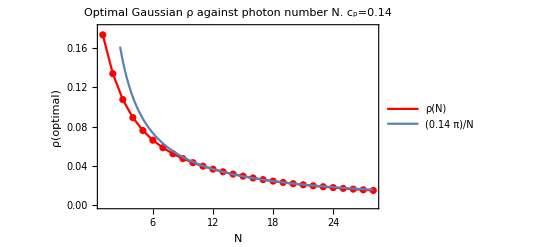

```mathematica
Show[ListPlot[ρNphπ, PlotStyle->Red,PlotLabel->"Optimal Gaussian ρ against photon number N. c_p=0.14"],ListLinePlot[ρNphπ, PlotStyle->Red,PlotLegends->{"ρ(N)"}], Plot[{bestfitρlineNph}, {x, 1,28},PlotLegends->{"(0.14  π)/N"}],PlotRange->{{1,28},{0,0.18}}, Frame->True,FrameLabel->{"N","ρ(optimal)"}]
```

```mathematica
0.18445912644648962/π
```

0.0587152

```mathematica
0.23/π
```

0.0732113

### Showing that ρ ∝ Δ for 1 shot

#### Setting nph = 7, and varying Δ from 0 to π

```mathematica
GetVariance[1,7];
```

```mathematica
(*Get all optimal ρ*)
Listρ7 = PlugG2[];
Listρ = Table[Listρ7[[n,1,2]],{n,1,10}];
(*Eliminating the N00N regime*)
Listρ=Take[Listρ,-8];
(*Construct the x axis for plotting*)
Listx = Table[(n π)/10,{n,3,10}];
(*Listρ vs Listx*)
ρfunc = Thread[{Listx,Listρ}];
(*Best-fit line*)
bestfitρline=Fit[ρfunc,{1,x},x];
```

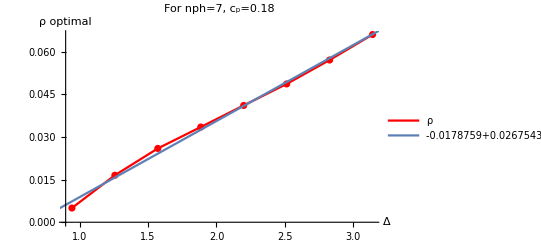

```mathematica
Show[ListPlot[ρfunc, PlotStyle->Red],ListLinePlot[ρfunc, PlotStyle->Red,PlotLegends->{"ρ"}], Plot[{bestfitρline}, {x, 0,10},PlotLegends->{bestfitρline}],AxesLabel-> {"Δ ","ρ optimal"},PlotLabel-> "For nph=7, c_p=0.18"]
```

```mathematica
(*ρ ≃ 0.026754259998803594Δ. Subscript[c, ρ] = (Nph*ρ)/Δ = 7* 0.026754259998803594*)
```

```mathematica
(*This is the proportionality constant Subscript[c, ρ]*)
```

```mathematica
0.026754259998803594*7
```

0.18728

#### Setting nph = 29, and varying Δ from 0 to π

```mathematica
GetVariance[1,29];
```

```mathematica
(*Get all optimal ρ*)
Listρ29 = PlugG2[];
Listρ29 = Table[Listρ29[[n,1,2]],{n,1,10}];
(*Eliminating the N00N regime*)
Listρ29=Take[Listρ29,-8];
(*Construct the x axis for plotting*)
Listx29 = Table[(n π)/10,{n,3,10}];
(*Listρ vs Listx*)
ρfunc29 = Thread[{Listx29,Listρ29}];
(*Best-fit line*)
bestfitρline29=Fit[ρfunc29,{1,x},x];
```

```mathematica
bestfitρline29=0.13x/29
```

0.00448276 x

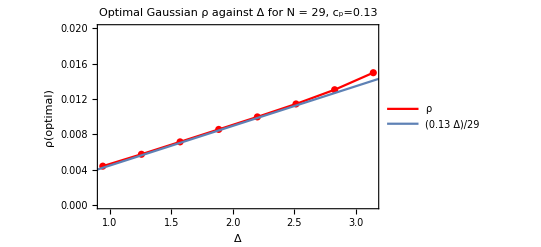

```mathematica
Show[ListPlot[ρfunc29, PlotStyle->Red],ListLinePlot[ρfunc29, PlotStyle->Red,PlotLegends->{"ρ"}], Plot[{bestfitρline29}, {x, 0,10},PlotLegends->{"(0.13  Δ)/29"}],AxesLabel-> {"Δ ","ρ optimal"},PlotLabel-> "Optimal Gaussian ρ against Δ for N = 29, c_p=0.13",PlotRange->{{(3 π)/10,π},{0,0.02}}, Frame->True,FrameLabel->{"Δ","ρ(optimal)"}]
```

```mathematica
(*ρ ≃ 0.0047242839776750175Δ. Subscript[c, ρ] = (Nph*ρ)/Δ = 29* 0.0047242839776750175*)
```

```mathematica
(*This is the proportionality constant Subscript[c, ρ]*)
```

```mathematica
0.0047242839776750175*29
```

0.137004

## 5. Show that ρ≃c_p Δ/Nwhere c_p≃0.16 is a good approximation

### Compare ratio of variance (Nph) of Optimized Gaussian with Approximate Gaussian for Δ = π, varying Nph (1-> 20)

```mathematica
num=20;
VarRatio=Table[
GetVariance[1,n];
List[GetOpt[],PlugG1[],PlugG2[]]
,{n,1,num}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
VarRatio={{{0.507232851775152},{0.5072328517751518},{0.5072328517751519}},{{0.3236361883875709},{0.3276187462394842},{0.323636188387695}},{{0.23232846432806875},{0.23415719135391166},{0.23232846432796073}},{{0.17912299685903402},{0.18051271598530066},{0.17956154629861704}},{{0.14479559308539766},{0.14641164229692513},{0.14584317292603297}},{{0.12102135384645674},{0.12303296980436447},{0.1226584083579695}},{{0.1036680796795774},{0.10605844251022882},{0.10579467673583214}},{{0.09048185660078893},{0.09317260287066699},{0.09297726476964777}},{{0.08014144308773866},{0.08304146504335361},{0.08288972698604585}},{{0.07182619366477512},{0.07485135807749695},{0.0747271713613476}},{{0.06500132954988616},{0.06808157758727455},{0.06797383289843441}},{{0.059304076796392366},{0.06238495912833104},{0.06228556890815272}},{{0.054479908600181},{0.057521497776084896},{0.05742426763086888}},{{0.05034509965906326},{0.05331984747822282},{0.05321977474303513}},{{0.0467637858009579},{0.04965410501729526},{0.04954694550360781}},{{0.04363338300617598},{0.04642936162541256},{0.04631138539072214}},{{0.040875020079502895},{0.04357243885146732},{0.04344031151820924}},{{0.038427085415023196},{0.041025790618616845},{0.04087653184717212}},{{0.03624076782916042},{0.038743385903371105},{0.03857436741546748}},{{0.034276908843555526},{0.03668786227868532},{0.03649682043888073}}}
```

{{{0.507233},{0.507233},{0.507233}},{{0.323636},{0.327619},{0.323636}},{{0.232328},{0.234157},{0.232328}},{{0.179123},{0.180513},{0.179562}},{{0.144796},{0.146412},{0.145843}},{{0.121021},{0.123033},{0.122658}},{{0.103668},{0.106058},{0.105795}},{{0.0904819},{0.0931726},{0.0929773}},{{0.0801414},{0.0830415},{0.0828897}},{{0.0718262},{0.0748514},{0.0747272}},{{0.0650013},{0.0680816},{0.0679738}},{{0.0593041},{0.062385},{0.0622856}},{{0.0544799},{0.0575215},{0.0574243}},{{0.0503451},{0.0533198},{0.0532198}},{{0.0467638},{0.0496541},{0.0495469}},{{0.0436334},{0.0464294},{0.0463114}},{{0.040875},{0.0435724},{0.0434403}},{{0.0384271},{0.0410258},{0.0408765}},{{0.0362408},{0.0387434},{0.0385744}},{{0.0342769},{0.0366879},{0.0364968}}}

```mathematica
num=20
```

20

```mathematica
VarRatioOptπ = Table[VarRatio[[n,1,1]],{n,1,num}];
VarRatioG1π = Table[VarRatio[[n,2,1]],{n,1,num}];
VarRatioG2π = Table[VarRatio[[n,3,1]],{n,1,num}];
```

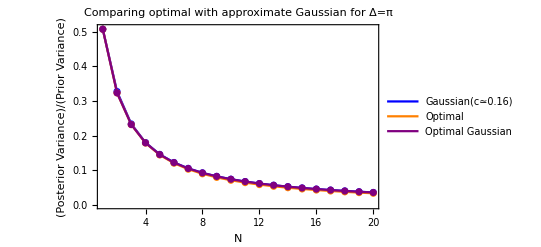

```mathematica
Show[ListPlot[VarRatioG1π,PlotStyle->Blue],ListLinePlot[VarRatioG1π,PlotLegends->{"Gaussian(c≃0.16)"},PlotStyle->Blue],ListPlot[VarRatioOptπ,PlotStyle->Orange],ListLinePlot[VarRatioOptπ,PlotLegends->{"Optimal"},PlotStyle->Orange],ListPlot[VarRatioG2π,PlotStyle->Purple],ListLinePlot[VarRatioG2π,PlotLegends->{"Optimal Gaussian"},PlotStyle->Purple],AxesOrigin->{0,0},PlotRange->{{1,20},{0,0.51}}, Frame->True,FrameLabel->{"N","(Posterior Variance)/(Prior Variance)"}, PlotLabel-> "Comparing optimal with approximate Gaussian for Δ=π"]
```

## 6. Plugging in generic N00N and Gaussian states and comparing variance for 1 shot

### Compare ratio of variance (Nph) of Gaussian using formula, N00N using formula, and optimized state for Δ = 3π/10, varying Nph (1-> 20)

```mathematica
num=20;
VarRatio2=Table[
GetVariance[1,n];
List[GetOpt[],PlugG1[],PlugN00N[],PlugG2[]]
,{n,1,num}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{{0.929204},{0.929204},{0.929204},{0.929204}},{{0.752679},{0.840366},{0.752679},{0.83463}},{{0.558699},{0.747539},{0.558699},{0.738554}},{{0.441135},{0.657654},{0.441135},{0.646414}},{{0.415779},{0.575218},{0.451798},{0.563582}},{{0.375555},{0.5027},{0.578076},{0.492878}},{{0.342757},{0.439827},{0.756251},{0.432132}},{{0.325367},{0.387387},{0.909963},{0.382211}},{{0.327684},{0.3429},{0.990078},{0.339225}},{{0.294354},{0.306159},{0.993916},{0.303774}},{{0.265198},{0.275088},{0.956264},{0.273449}},{{0.241057},{0.248867},{0.921805},{0.247694}},{{0.220139},{0.226466},{0.917934},{0.225556}},{{0.202245},{0.207233},{0.943646},{0.206482}},{{0.186472},{0.190541},{0.977872},{0.189861}},{{0.172923},{0.1761},{0.998235},{0.175479}},{{0.160844},{0.163445},{0.996342},{0.162847}},{{0.150226},{0.152349},{0.98054},{0.151765}},{{0.14075},{0.142549},{0.966813},{0.141966}},{{0.132264},{0.133844},{0.966226},{0.133253}}}

```mathematica
VarRatioOpt3π10 = Table[VarRatio2[[n,1,1]],{n,1,num}];
VarRatioG13π10 = Table[VarRatio2[[n,2,1]],{n,1,num}];
VarRatioN00N3π10 = Table[VarRatio2[[n,3,1]],{n,1,num}];
VarRatioG23π10 = Table[VarRatio2[[n,4,1]],{n,1,num}];
```

```mathematica
yequal13=Table[1,num];
```

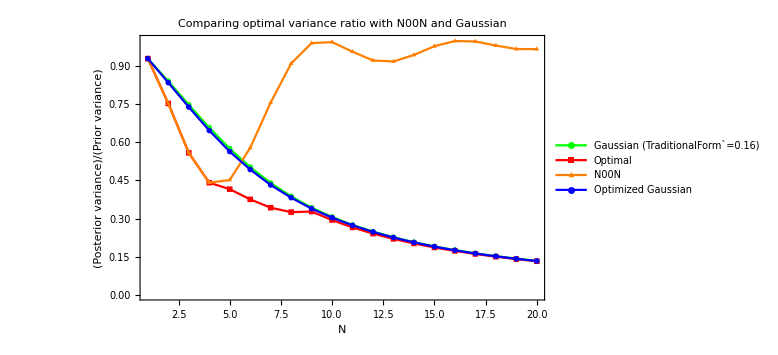

```mathematica
Show[ListLinePlot[VarRatioG13π10,PlotMarkers ->{"x",Scaled[0.03]},PlotLegends->Placed[{"Gaussian (TraditionalForm`=0.16)"},{0.8,0.5}],PlotStyle->Green],ListLinePlot[VarRatioOpt3π10,PlotMarkers ->{■,Scaled[0.05]},PlotLegends->Placed[{"Optimal"},{0.8,0.7}],PlotStyle->Red],ListLinePlot[VarRatioN00N3π10,PlotMarkers ->{▲,Scaled[0.05]},PlotLegends->Placed[{"N00N"},{0.8,0.6}],PlotStyle->Orange],ListLinePlot[VarRatioG23π10,PlotMarkers ->{"†",Scaled[0.03]},PlotLegends->Placed[{"Optimized Gaussian"},{0.8,0.4}],PlotStyle->Blue],AxesOrigin-> {0,0}, PlotLabel-> "Comparing optimal variance ratio with N00N and Gaussian" ,FrameLabel->{"N","(Posterior variance)/(Prior variance)"}, PlotRange->{{1,num},{0,1}},Frame->True,ImageSize->Large]
```

## 7. Gaussian vs N00N

```mathematica
nph=3
```

3

```mathematica
ns=1
```

1

```mathematica
Clear[ρ3]
```

```mathematica
ρ3 = Table[Symbol["ρ3s"<>ToString[n]],{n,1,ns}];
ψG2r =Table[Table[(E^(-ρ3[[n]](k-nph/2)^2))/(√(∑_(kprime=0)^nph (E^(-ρ3[[n]](kprime-nph/2)^2))^2)),{k,0,nph}],{n,1,ns}];
ψG2θ=Table[Table[ k (π/2),{k,0,nph}],{n,1,ns}];
```

```mathematica
ψQG2r =Table[(E^(-ρ2(k-nph/2)^2-ρprime2(k-nph/2)^4))/(√(∑_(kprime=0)^nph (E^(-ρ2(kprime-nph/2)^2-ρprime2(kprime-nph/2)^4))^2)),{k,0,nph}];
ψQG2θ=Table[ k (π/2),{k,0,nph}];
```

```mathematica
ψG2r/.ρ3s1-> -x
```

{{ⅇ^(9 x/4)/(√(2 ⅇ^(x/2)+2 ⅇ^(9 x/2))),ⅇ^(x/4)/(√(2 ⅇ^(x/2)+2 ⅇ^(9 x/2))),ⅇ^(x/4)/(√(2 ⅇ^(x/2)+2 ⅇ^(9 x/2))),ⅇ^(9 x/4)/(√(2 ⅇ^(x/2)+2 ⅇ^(9 x/2)))}}

```mathematica
(E^(-ρ3(k-nph/2)^2))/(√(∑_(kprime=0)^nph (E^(-ρ3(kprime-nph/2)^2))^2))/.k->2
```

1/(√(1+2 ⅇ^(-8 ρ3)+2 ⅇ^(-2 ρ3)))